# Checking c2 ratios in Higgs to Zγ loops

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## SM Results

decayRate = (1/(32*Pi*mh))*PolarizationSum[matSQ]

```mathematica
diphotonSMDR = 0.0000092389 (*from the PDG*)
```

9.2389×10^-6

```mathematica
diphotonSMAmp = -1*Sqrt[diphotonSMDR*(32*Pi*mh)/(2)] /.mh-> 125 (*the 2 and -1 are from the polarization sum and taking the w boson loop's domination into account*)
```

-0.240935

```mathematica
gammaZSMDR = 0.0000062271 (*from the PDG*)
```

6.2271×10^-6

```mathematica
gammaZSMAmp = -1*Sqrt[diphotonSMDR*(8*Pi*mh^2)/(2*(Sqrt[mh^4+mZ^4-2mh^2 mZ^2]/(2*mh)))] /.mh-> 125 /.mZ-> 90.2(*the 2 and -1 are from the polarization sum and taking the w boson loop's domination into account*)
```

-0.246085

```mathematica
digluonSMDR = 0.000348799
```

0.000348799

```mathematica
digluonSMAmp = Sqrt[digluonSMDR*(32*Pi*mh)/(2)] /.mh-> 125 (*the 2 is from the polarization sum*)
```

1.48039

## Regions

```mathematica
oneSig =Polygon[{{0.579,1.310},{0.580,1.287},{0.584,1.269},{0.588,1.253},{0.593,1.238},{0.599,1.225},{0.607,1.211},{0.615,1.196},{0.624,1.182},{0.633,1.167},{0.643,1.154},{0.652,1.142},{0.662,1.131},{0.672,1.120},{0.681,1.110},{0.691,1.100},{0.700,1.091},{0.710,1.082},{0.720,1.074},{0.729,1.066},{0.739,1.058},{0.748,1.051},{0.758,1.044},{0.767,1.036},{0.777,1.030},{0.787,1.024},{0.796,1.017},{0.806,1.011},{0.815,1.006},{0.825,1.000},{0.835,0.995},{0.844,0.989},{0.854,0.984},{0.863,0.980},{0.873,0.976},{0.882,0.971},{0.892,0.967},{0.902,0.963},{0.911,0.960},{0.921,0.956},{0.930,0.953},{0.940,0.950},{0.949,0.947},{0.959,0.945},{0.969,0.944},{0.978,0.943},{0.988,0.941},{0.997,0.940},{1.007,0.941},{1.017,0.942},{1.026,0.944},{1.036,0.947},{1.045,0.953},{1.048,0.964},{1.046,0.975},{1.040,0.992},{1.031,1.007},{1.022,1.020},{1.013,1.034},{1.004,1.046},{0.994,1.058},{0.984,1.070},{0.975,1.081},{0.965,1.092},{0.956,1.103},{0.946,1.113},{0.936,1.124},{0.927,1.134},{0.917,1.144},{0.908,1.154},{0.898,1.164},{0.889,1.174},{0.879,1.184},{0.869,1.194},{0.860,1.203},{0.850,1.213},{0.841,1.222},{0.831,1.231},{0.821,1.240},{0.812,1.249},{0.802,1.258},{0.793,1.267},{0.783,1.275},{0.774,1.283},{0.764,1.290},{0.754,1.298},{0.745,1.305},{0.735,1.312},{0.726,1.320},{0.716,1.326},{0.706,1.333},{0.697,1.339},{0.687,1.345},{0.678,1.351},{0.668,1.356},{0.659,1.360},{0.649,1.363},{0.639,1.365},{0.630,1.367},{0.620,1.366},{0.611,1.364},{0.601,1.360},{0.592,1.350},{0.584,1.333}}];
twoSig=Polygon[{{0.470,1.376},{0.472,1.352},{0.476,1.328},{0.480,1.305},{0.486,1.283},{0.494,1.262},{0.503,1.242},{0.511,1.222},{0.521,1.204},{0.532,1.186},{0.543,1.168},{0.554,1.152},{0.567,1.136},{0.579,1.121},{0.591,1.106},{0.604,1.092},{0.616,1.078},{0.629,1.065},{0.643,1.053},{0.656,1.041},{0.670,1.029},{0.684,1.017},{0.698,1.006},{0.712,0.995},{0.726,0.984},{0.740,0.975},{0.755,0.965},{0.770,0.956},{0.784,0.947},{0.798,0.937},{0.813,0.930},{0.828,0.922},{0.843,0.913},{0.858,0.906},{0.872,0.898},{0.887,0.891},{0.902,0.883},{0.917,0.878},{0.933,0.871},{0.947,0.864},{0.963,0.858},{0.978,0.853},{0.993,0.847},{1.008,0.841},{1.024,0.835},{1.039,0.831},{1.054,0.827},{1.070,0.822},{1.085,0.818},{1.101,0.814},{1.116,0.810},{1.132,0.807},{1.147,0.804},{1.163,0.802},{1.179,0.799},{1.194,0.796},{1.210,0.794},{1.225,0.791},{1.241,0.792},{1.257,0.792},{1.273,0.791},{1.288,0.794},{1.303,0.799},{1.312,0.816},{1.308,0.838},{1.299,0.854},{1.291,0.864},{1.283,0.873},{1.273,0.884},{1.260,0.898},{1.247,0.911},{1.235,0.924},{1.226,0.933},{1.218,0.940},{1.207,0.950},{1.194,0.963},{1.180,0.975},{1.167,0.987},{1.155,1.000},{1.144,1.009},{1.137,1.015},{1.126,1.025},{1.114,1.037},{1.105,1.045},{1.097,1.052},{1.086,1.062},{1.073,1.075},{1.060,1.088},{1.047,1.100},{1.033,1.113},{1.021,1.126},{1.011,1.134},{1.004,1.141},{0.993,1.152},{0.980,1.165},{0.967,1.178},{0.955,1.190},{0.945,1.199},{0.937,1.206},{0.927,1.216},{0.914,1.229},{0.901,1.242},{0.889,1.255},{0.879,1.264},{0.871,1.270},{0.861,1.281},{0.848,1.294},{0.835,1.307},{0.821,1.319},{0.812,1.328},{0.804,1.335},{0.794,1.345},{0.781,1.357},{0.768,1.369},{0.757,1.379},{0.750,1.384},{0.740,1.393},{0.727,1.405},{0.713,1.416},{0.699,1.427},{0.688,1.436},{0.681,1.440},{0.670,1.449},{0.658,1.458},{0.652,1.461},{0.641,1.468},{0.629,1.475},{0.623,1.478},{0.612,1.484},{0.597,1.490},{0.581,1.495},{0.565,1.498},{0.549,1.498},{0.534,1.495},{0.519,1.489},{0.505,1.478},{0.493,1.464},{0.483,1.445},{0.476,1.424},{0.472,1.400}}];
```

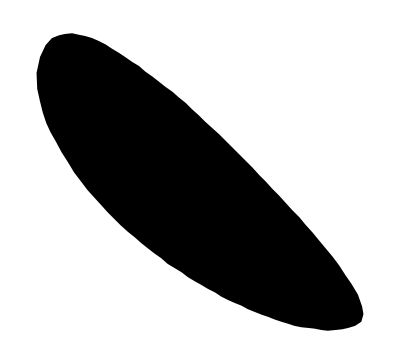

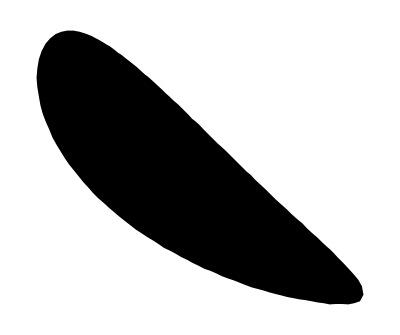

```mathematica
oneSigReg=Region[oneSig]
twoSigReg=Region[twoSig]
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (Z or photon)
p2= Momentum of 2nd out-going particle (photon)
mh= Mass of the decaying higgs
m = Mass of the stop
ghss= Higgs-stop coupling
α = Fine structure constant
x and y are Feynman parameters

Additional notation for the Zγ decay:
m1= Mass of the lighter stop mass eignestate
m2= Mass of the heavier stop mass eigenstate
zij= Coupling of the Z boson to stops of mass eigenstates ij = 11, 12, 21, 22
zgij= 4 point coupling of the Z boson and a photon to the stop mass eigenstates
hij= Higgs coupling to stops in their mass eigenstates (note: h11= ghSS)

After introducing all LO and NLO coefficients in this language, I will introduce the explicit dependence of these factors on MSSM parameters. See my summary Latex document for more details.

## Higgs to diphoton (on-shell, via stop loop)

```mathematica
matSqDP =Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]]/.c2->c2DP(*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details*)
```

(9 (c2DP^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)+6 c1 c2DP (mg1^2+mg2^2-mh^2) mZ^2+8 c1^2 mZ^4))/(2 v^2)

```mathematica
matSqZg =Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]]/.c2->c2Zg(*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details*)
```

(9 (c2Zg^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)+6 c1 c2Zg (mg1^2+mg2^2-mh^2) mZ^2+8 c1^2 mZ^4))/(2 v^2)

The c1 on-shell term is zero.

```mathematica
c2LOggIntedDP = 2*(Rational[1, 18]*e^2*ghSS*v*
     (mh^2 - 4*m1^2*ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2))/(mh^4*Pi^2)
```

(e^2 ghSS v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2))/(9 mh^4 π^2)

```mathematica
c2LOzgMixInted=2*Times[v,Plus[Times[Rational[1,12],e,Power[Pi,-2],Subscript[h,11],Power[Subscript[m,h],-1],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Power[Subscript[m,h],3],Times[-2,ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[1,2]],Power[Subscript[m,Z],2]],Times[-1,Subscript[m,h],Plus[Times[4,Power[m1,2],Plus[Power[ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],2]]]],Power[Subscript[m,Z],2],Times[-2,ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[1,2]]]]]],Subscript[z,11]],Times[Rational[-1,12],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Power[Subscript[m,h],-4],Plus[Times[-1,Log[Power[m2,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,h],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]],Times[-1,Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[Subscript[m,Z],-2],Plus[Times[Log[Power[m2,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,Z],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]],Subscript[z,12]],Times[Rational[-1,12],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Power[Subscript[m,h],-4],Plus[Times[-1,Log[Power[m1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,h],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]],Times[-1,Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[Subscript[m,Z],-2],Plus[Times[Log[Power[m1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,Z],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]],Subscript[z,12]],Times[Rational[1,6],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m2,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2],Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m2,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2],Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],2]],Rational[1,2]]],-1]]]]],Power[Subscript[m,h],2],Times[Rational[1,2],Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]],Times[-1,Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2]],Times[Rational[-1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]]],Times[Rational[-1,2],Log[Power[m1,2]],Power[Subscript[m,h],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Subscript[m,h],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,h],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Plus[Times[-1,Power[Subscript[m,h],2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]],Times[-1,Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Log[Power[m1,2]],Power[Subscript[m,Z],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Subscript[m,Z],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,Z],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]]]],Subscript[z,12]],Times[Rational[1,6],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m1,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,h],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2],Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,h],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m1,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,Z],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2],Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,Z],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],2]],Rational[1,2]]],-1]]]]],Power[Subscript[m,h],2],Times[Rational[1,2],Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]],Times[-1,Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2]],Times[Rational[-1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,h],-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]]],Times[Rational[-1,2],Log[Power[m2,2]],Power[Subscript[m,h],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Subscript[m,h],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,h],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Plus[Times[-1,Power[Subscript[m,h],2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]],Times[-1,Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,Z],-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Log[Power[m2,2]],Power[Subscript[m,Z],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Subscript[m,Z],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,Z],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]]]],Subscript[z,12]],Times[Rational[1,12],e,Power[Pi,-2],Subscript[h,22],Power[Subscript[m,h],-1],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Power[Subscript[m,h],3],Times[-2,ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[1,2]],Power[Subscript[m,Z],2]],Times[-1,Subscript[m,h],Plus[Times[4,Power[m2,2],Plus[Power[ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],2]]]],Power[Subscript[m,Z],2],Times[-2,ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[1,2]]]]]],Subscript[z,22]]]]/.Subscript[h, 11]-> h11/.Subscript[z, 11]-> z11 /.Subscript[h, 12]->h12/.Subscript[z, 12]-> z12/.Subscript[h, 22]-> h22/.Subscript[z, 22]->z22/.Subscript[zg, 11]-> zg11/.Subscript[zg, 12]->zg12/.Subscript[zg, 22]->zg22/.Subscript[M, 1]-> M1/.Subscript[M, 2]-> M2/. Subscript[m, h]-> mh /.Subscript[m, Z]-> mZ;
```

## Higgs to gg

```mathematica
matSqDG =(2/9)*(9/4)^2*Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]]/.c2->c2DG(*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details. Adjustments for the differences between the diphoton and digluon case can be seen in front of the "Times[]" bracket.*)
```

(81 (c2DG^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)+6 c1 c2DG (mg1^2+mg2^2-mh^2) mZ^2+8 c1^2 mZ^4))/(16 v^2)

The c1 on-shell term is zero.

```mathematica
c2LOggIntedDG = 2*(Rational[1, 18]*gs^2*ghSS*v*
     (mh^2 - 4*m1^2*ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2))/(mh^4*Pi^2)
```

(ghSS gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2))/(9 mh^4 π^2)

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2+2 c ct st+b st^2

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

b ct^2-2 c ct st+a st^2

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ Cot[β]))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
Alfas->0.12,Alfas2-> (0.12^2),
gs-> Sqrt[4*Pi*Alfas],
sW->0.4720,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
v-> 246,
m1->stopMass1,m2-> stopMass2,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

## Plug in values

```mathematica
c2LOggIntedDP2 = c2LOggIntedDP /. ghSS -> ghSS2/.m1-> m2;
c2LOggIntedDG2 = c2LOggIntedDG /. ghSS -> ghSS2/.m1->m2;
```

```mathematica
c1 = 0;
c2DP =c2LOggIntedDP + c2LOggIntedDP2//. ghSS-> h11//.ghSS2-> h22
c2DG =c2LOggIntedDG + c2LOggIntedDG2//. ghSS-> h11//.ghSS2 -> h22
c2Zg =c2LOzgMixInted;
```

(e^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(e^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)

(gs^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)

```mathematica
matSqDP
```

1/(2 v^2)9 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2) ((e^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(e^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2))^2

```mathematica
matSqDG
```

1/(16 v^2)81 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2) ((gs^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2))^2

```mathematica
matSqZg;
```

```mathematica
osMatSqDP = matSqDP /. mg1 -> 0 /. mg2 -> 0
osMatSqDG = matSqDG /. mg1 -> 0 /. mg2 -> 0
osMatSqZg = matSqZg /. mg1 -> 0 /. mg2 -> 0;
```

1/(2 v^2)9 mh^4 ((e^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(e^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2))^2

1/(16 v^2)81 mh^4 ((gs^2 v (mh^2-4 m2^2 ArcTan[mh/(√(4 m2^2-mh^2))]^2) (ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)+(gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2))^2

```mathematica
myCalcResultDP = osMatSqDP//.SUBIN[m1,m2,xt,250,1.47]//Simplify
myCalcResultDG = osMatSqDG//.SUBIN[m1,m2,xt,250,1.47]//Simplify
myCalcResultZg = osMatSqZg//.SUBIN[m1,m2,xt,250,1.47];
```

1/(4500000000000 π^2)((15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+(15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2

1/107584 2197265625 (1.71058×10^-8 (15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+1.71058×10^-8 (15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2

```mathematica
bsmDPAmp =Sqrt[myCalcResultDP]/2
bsmDGAmp =Sqrt[myCalcResultDG]/2
bsmZgAmp =Sqrt[myCalcResultZg]/2;
```

1/(3000000 √2 π)(√((15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+(15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2)

46875/656 √(1.71058×10^-8 (15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+1.71058×10^-8 (15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2

```mathematica
totDPAmp =bsmDPAmp + diphotonSMAmp
totDGAmp =bsmDGAmp + digluonSMAmp
totZgAmp =bsmZgAmp + gammaZSMAmp;
```

-0.240935+1/(3000000 √2 π)(√((15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+(15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2)

1.48039+46875/656 √(1.71058×10^-8 (15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+1.71058×10^-8 (15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2

```mathematica
totDPDR = (1/(32*Pi*mh))*2*totDPAmp^2 /. mh->125
totDGDR = (1/(32*Pi*mh))*2*totDGAmp^2 /. mh->125
totZgDR = ((Sqrt[mh^4+mZ^4-2mh^2 mZ^2]/(2mh))/(8*Pi*mh^2))*2*totZgAmp^2 /. mh->125/.mZ-> 90.2;
```

1/(2000 π)(-0.240935+1/(3000000 √2 π)(√((15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+(15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2))^2

1/(2000 π)(1.48039+46875/656 √(1.71058×10^-8 (15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((247.112 xt^2)/(m1^2-1. m2^2)-(6.68804×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)+1.71058×10^-8 (15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(247.112 xt^2)/(m1^2-1. m2^2)-(7.09674×10^6 xt^2 Csc[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[(346 xt)/(m1^2-m2^2)]]^2))^2)^2

```mathematica
kGamma = (totDPDR/diphotonSMDR)^(1/2)/.xt-> ((m1^2 -m2^2)/(2*173))*Sin[2*θ]
```

4.1505 √(-0.240935+1/(3000000 √2 π)(√((15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((0.00206415 (m1^2-m2^2)^2 Sin[2 θ]^2)/(m1^2-1. m2^2)-(55.8659 (m1^2-m2^2)^2 Csc[1/2 ArcSin[Sin[2 θ]]]^2 Sin[2 θ]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[Sin[2 θ]]]^2)+(15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(0.00206415 (m1^2-m2^2)^2 Sin[2 θ]^2)/(m1^2-1. m2^2)-(59.2798 (m1^2-m2^2)^2 Csc[1/2 ArcSin[Sin[2 θ]]]^2 Sin[2 θ]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[Sin[2 θ]]]^2))^2))^2

```mathematica
kGlue = (totDGDR/digluonSMDR)^(1/2) /.xt-> ((m1^2 -m2^2)/(2*173))*Sin[2*θ]
```

0.675495 √(1.48039+46875/656 √(1.71058×10^-8 (15625-4 m1^2 ArcTan[125/(√(-15625+4 m1^2))]^2) ((0.00206415 (m1^2-m2^2)^2 Sin[2 θ]^2)/(m1^2-1. m2^2)-(55.8659 (m1^2-m2^2)^2 Csc[1/2 ArcSin[Sin[2 θ]]]^2 Sin[2 θ]^2)/((m1^2-1. m2^2)^2)-237.119 Sin[1/2 ArcSin[Sin[2 θ]]]^2)+1.71058×10^-8 (15625-4 m2^2 ArcTan[125/(√(-15625+4 m2^2))]^2) (-(0.00206415 (m1^2-m2^2)^2 Sin[2 θ]^2)/(m1^2-1. m2^2)-(59.2798 (m1^2-m2^2)^2 Csc[1/2 ArcSin[Sin[2 θ]]]^2 Sin[2 θ]^2)/((m1^2-1. m2^2)^2)-223.464 Sin[1/2 ArcSin[Sin[2 θ]]]^2))^2)^2

## Checking c2 ratios

```mathematica
c2TR=c2Zg//.SUBIN[m1,m2,xt,250,1.47];
```

```mathematica
c2NM = (3/Sqrt[2])*c2TR /. xt -> 0.00001 ;(*The 3/sqrt2 is to account for colour and polariztion factors*)
```

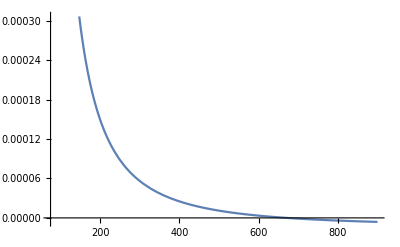

```mathematica
Plot[(c2NM/.m1-> 1000),{m2,75,900}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

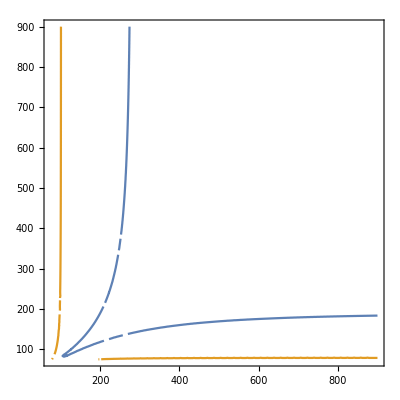

```mathematica
ContourPlot[{Abs[c2NM/0.018]==.01,Abs[c2NM/0.018]==0.1},{m1,75,900},{m2,75,900},PlotPoints->50]
```

## Parameter Space Scan

```mathematica
kGammaRes[stop1_,stop2_,mixt_] := kGamma /. θ -> mixt /. m1-> stop1 /. m2-> stop2
kGlueRes [stop1_,stop2_,mixt_] := kGlue /. θ -> mixt /. m1-> stop1 /. m2-> stop2
```

```mathematica
regMemFunc1S2[m1_,m2_,tt_]:=If[RegionMember[oneSigReg,{kGlueRes[m1,m2,tt],kGammaRes[m1,m2,tt]}],inRange1 =1,inRange1 = 0]
regMemFunc2S2[m1_,m2_,tt_]:=If[RegionMember[twoSigReg,{kGlueRes[m1,m2,tt],kGammaRes[m1,m2,tt]}],inRange2 =1,inRange2 = 0]
```

```mathematica
stream=OpenAppend["C2ValuesZg.txt",FormatType->StandardForm];
Write[stream, "scan   m1   m2    angle    c2Ratio" ];
bigR = 0;
```

```mathematica
C2Values[x_,y_,z_,num_]:=Module[{k=num},
If[regMemFunc2S2[x,y,z]==0,Continue[]];

AZg=0.014;
c2TR=c2Zg//.SUBIN[x,y,z,250,1.47];
c2NM = (3/Sqrt[2])*c2TR ;
c2ratio = Abs[c2NM/AZg];
If[c2ratio>bigR,bigR=c2ratio];

If[c2ratio<0.03,Continue[]];

Write[stream,k," ",x, " ", y," ", z, " ",c2ratio ];
If[Mod[k,1000]==0, Print[k]];
(*Print[c2ratio];
Print[bigR];*)
]
```

```mathematica
For[x = 1,x<10001,x++,rv2 = RandomVariate[UniformDistribution[{100, 500}]];rv1 = RandomVariate[UniformDistribution[{100, rv2}]];rv3 = RandomVariate[UniformDistribution[{-Pi/2, Pi/2}]];C2Values[rv1,rv2,rv3,x]]
Close[stream]
```

C2ValuesZg.txt

```mathematica
bigR
```

0.0593505